# Fourier trigonometric series expansion

```mathematica
Needs["FourierSeries`"]
```

```mathematica
Clear["Global`*"]
```

## Trigonometric representation

```mathematica
order=20;
```

```mathematica
f=UnitBox[x] ;
```

```mathematica
fts=FourierTrigSeries[f,x,order]
```

1/(2 π)+(2 Cos[x] Sin[1/2])/π+(Cos[2 x] Sin[1])/π+(2 Cos[3 x] Sin[3/2])/(3 π)+(Cos[4 x] Sin[2])/(2 π)+(2 Cos[5 x] Sin[5/2])/(5 π)+(Cos[6 x] Sin[3])/(3 π)+(2 Cos[7 x] Sin[7/2])/(7 π)+(Cos[8 x] Sin[4])/(4 π)+(2 Cos[9 x] Sin[9/2])/(9 π)+(Cos[10 x] Sin[5])/(5 π)+(2 Cos[11 x] Sin[11/2])/(11 π)+(Cos[12 x] Sin[6])/(6 π)+(2 Cos[13 x] Sin[13/2])/(13 π)+(Cos[14 x] Sin[7])/(7 π)+(2 Cos[15 x] Sin[15/2])/(15 π)+(Cos[16 x] Sin[8])/(8 π)+(2 Cos[17 x] Sin[17/2])/(17 π)+(Cos[18 x] Sin[9])/(9 π)+(2 Cos[19 x] Sin[19/2])/(19 π)+(Cos[20 x] Sin[10])/(10 π)

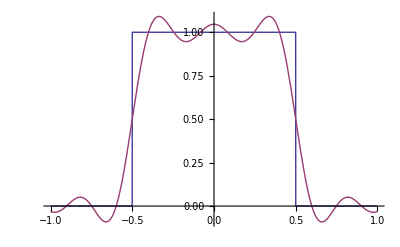

```mathematica
Plot[{f,fts},{x,-1,1}]
```

## Complex representation

```mathematica
fs=FourierSeries[f,x,order]
```

1/(2 π)+(ⅇ^(-ⅈ x) Sin[1/2])/π+(ⅇ^(ⅈ x) Sin[1/2])/π+(ⅇ^(-2 ⅈ x) Sin[1])/(2 π)+(ⅇ^(2 ⅈ x) Sin[1])/(2 π)+(ⅇ^(-3 ⅈ x) Sin[3/2])/(3 π)+(ⅇ^(3 ⅈ x) Sin[3/2])/(3 π)+(ⅇ^(-4 ⅈ x) Sin[2])/(4 π)+(ⅇ^(4 ⅈ x) Sin[2])/(4 π)+(ⅇ^(-5 ⅈ x) Sin[5/2])/(5 π)+(ⅇ^(5 ⅈ x) Sin[5/2])/(5 π)+(ⅇ^(-6 ⅈ x) Sin[3])/(6 π)+(ⅇ^(6 ⅈ x) Sin[3])/(6 π)+(ⅇ^(-7 ⅈ x) Sin[7/2])/(7 π)+(ⅇ^(7 ⅈ x) Sin[7/2])/(7 π)+(ⅇ^(-8 ⅈ x) Sin[4])/(8 π)+(ⅇ^(8 ⅈ x) Sin[4])/(8 π)+(ⅇ^(-9 ⅈ x) Sin[9/2])/(9 π)+(ⅇ^(9 ⅈ x) Sin[9/2])/(9 π)+(ⅇ^(-10 ⅈ x) Sin[5])/(10 π)+(ⅇ^(10 ⅈ x) Sin[5])/(10 π)+(ⅇ^(-11 ⅈ x) Sin[11/2])/(11 π)+(ⅇ^(11 ⅈ x) Sin[11/2])/(11 π)+(ⅇ^(-12 ⅈ x) Sin[6])/(12 π)+(ⅇ^(12 ⅈ x) Sin[6])/(12 π)+(ⅇ^(-13 ⅈ x) Sin[13/2])/(13 π)+(ⅇ^(13 ⅈ x) Sin[13/2])/(13 π)+(ⅇ^(-14 ⅈ x) Sin[7])/(14 π)+(ⅇ^(14 ⅈ x) Sin[7])/(14 π)+(ⅇ^(-15 ⅈ x) Sin[15/2])/(15 π)+(ⅇ^(15 ⅈ x) Sin[15/2])/(15 π)+(ⅇ^(-16 ⅈ x) Sin[8])/(16 π)+(ⅇ^(16 ⅈ x) Sin[8])/(16 π)+(ⅇ^(-17 ⅈ x) Sin[17/2])/(17 π)+(ⅇ^(17 ⅈ x) Sin[17/2])/(17 π)+(ⅇ^(-18 ⅈ x) Sin[9])/(18 π)+(ⅇ^(18 ⅈ x) Sin[9])/(18 π)+(ⅇ^(-19 ⅈ x) Sin[19/2])/(19 π)+(ⅇ^(19 ⅈ x) Sin[19/2])/(19 π)+(ⅇ^(-20 ⅈ x) Sin[10])/(20 π)+(ⅇ^(20 ⅈ x) Sin[10])/(20 π)

```mathematica
Plot[{f,fs},{x,-1,1}]
```

-Graphics-

### Fourier coefficient

```mathematica
FourierCoefficient[f,x,n]
```

Sin[n/2]/(n π)